15

{{0,0},{0,1},{0,2},{0,3},{0,4},{1,0},{1,1},{1,2},{1,3},{2,0},{2,1},{2,2},{3,0},{3,1},{4,0}}

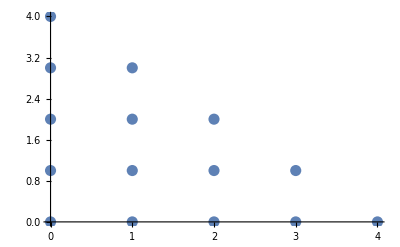

{1,y,y^2,y^3,y^4,x,x y,x y^2,x y^3,x^2,x^2 y,x^2 y^2,x^3,x^3 y,x^4}

```mathematica
n = 2; m = 4; μ = ((n+m)!)/(n!m!)
SS=Table[Subscript[S, i] = i, {i, 0, m}];
t={};i = 1; Do[If[j+k < m+1,{t=Join[t,{{Subscript[S, j],Subscript[S, k]}}],Subscript[ϕ, i][x_,y_] = x^Subscript[S, j] y^Subscript[S, k], i = i + 1}],{j,0,m},{k,0,m}]
t
ListPlot[t,PlotStyle->PointSize[0.02]]
Table[Subscript[ϕ, i][x,y],{i,1,μ}]
```

```mathematica
V=Table[Subscript[ϕ, j][t[[i,1]],t[[i,2]]],{i,1,μ},{j,1,μ}];
Det[V]≠0
```

True

```mathematica
eqv:=Table[∑_(i=1)^μ (Subscript[b, i] Subscript[ϕ, i][t[[k,1]],t[[k,2]]])==f[t[[k,1]],t[[k,2]]],{k,1,μ}]
koef:=Solve[eqv,{}]//Flatten

P[x_,y_]:=∑_(i=1)^μ (Subscript[b, i] Subscript[ϕ, i][x,y])/.koef
```

```mathematica
f[x_,y_] = 2^y*Cos[x+y];
P[x,y]//N
```

1.+0.169737 x-0.849278 x^2+0.2345 x^3-0.0146568 x^4-0.712498 y-0.724878 x y+0.139662 x^2 y+0.0293045 x^3 y+2.5554 y^2-2.01702 x y^2+0.403403 x^2 y^2-2.09194 y^3+0.716324 x y^3+0.329647 y^4

```mathematica
Table[P[t[[i,1]],t[[i,2]]]-f[t[[i,1]],t[[i,2]]],{i,1,μ}]//Simplify
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
mm = Min[SS]; MM  = Max[SS];
g1 = Plot3D[f[x, y], {x, mm, MM}, {y, mm, MM}];
g2 = Plot3D[P[x, y], {x, mm, MM}, {Ty, mm, MM}];
Tbl = Table[Point[{t[[i, 1]], t[[i, 2]], f[t[[i, 1]], t[[i, 2]]]}], {i, 1, μ}];
g3 = Graphics3D[{AbsolutePointSize[8],Tbl}];
Show[g1, g2, g3]
```

-Graphics3D-

```mathematica
Table[{f[x_,y_]=Subscript[ϕ, i][x,y],P[x,y]==Subscript[ϕ, i][x,y]},{i,1,μ}]
```

{{1,True},{y,True},{y^2,True},{y^3,True},{y^4,True},{x,True},{x y,True},{x y^2,True},{x y^3,True},{x^2,True},{x^2 y,True},{x^2 y^2,True},{x^3,True},{x^3 y,True},{x^4,True}}